```mathematica
ClearAll["Global`*"]
ρ=.25;
g=9.81;
BoatCurve[n_]:=2.0Abs[#/2]^n&;

BoatRegion[n_?NumericQ] := 
ImplicitRegion[
BoatCurve[n][y]<z<2 ,{{y,-2,2},{z,0,2}}
]

SubRegion[n_?NumericQ,θ_?NumericQ,b_?NumericQ]:=
ImplicitRegion[
BoatCurve[n][y]<z<2&&
Which[
θ ==Pi/2, y>b,
θ==3Pi/2,y<b,
0≤θ<Pi/2 || 3Pi/2<θ≤2Pi,z<Tan[θ]*y+b,
Pi/2<θ<3Pi/2,z>Tan[θ]*y+b
],
{{y,-2,2},{z,0,2}}]

mass[n_?NumericQ]:=ρ*NIntegrate[1,{y,z}∈BoatRegion[n]];
displacedMass[n_?NumericQ,θ_?NumericQ,b_?NumericQ]:=NIntegrate[1,{y,z}∈SubRegion[n,θ,b]]

b[n_?NumericQ,θ_?NumericQ]:=
b/.FindRoot[
mass[n]-displacedMass[n,θ,b],
{b,1}
]

EqRegion[n_?NumericQ,θ_?NumericQ]:=SubRegion[n,θ,b[n,θ]]

CoB[n_?NumericQ,θ_?NumericQ]:=ReleaseHold[Hold[NIntegrate[{y,z},{y,z}∈R]/NIntegrate[1,{y,z}∈R]]/.R-> Evaluate[EqRegion[n,θ]]] 
(*The arcane shit here is to make sure we only find b once, since that takes a long time*)

CoM[n_?NumericQ]:=(ρ*NIntegrate[{y,z},{y,z}∈BoatRegion[n]])/mass[n]

MomentArm[n_?NumericQ,θ_?NumericQ]:=(CoB[n,θ]-CoM[n])~Join~{0}

F[n_,θ_]:=({{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.{0,mass[n]*g})~Join~{0} 
(*this works because the boat is in equilibrium, and Buoyancy always points up from the waterline*)
T[n_,θ_] := -MomentArm[n,θ] ~ Cross~ F[n,θ] (*negative because theta is backwards*)
Tx[n_,θ_]:=T[n,θ][[3]]

nThetas=64;
thetas =Table [i,{i,0,2Pi,2Pi/(nThetas-1)}]//N;

Txs = Tx[2,#]&/@thetas
```

{0.,-0.366255,-0.768852,-1.24835,-1.8548,-2.65548,-3.74776,-5.04903,-5.84276,-6.18978,-6.18842,-5.9067,-5.39617,-4.69924,-3.8527,-2.88925,-1.8383,-0.726566,0.421389,1.58249,2.73452,3.85547,4.92264,5.91144,6.79345,7.53277,8.07884,8.35059,8.19596,7.26658,4.69006,1.54877,-1.54877,-4.69006,-7.26658,-8.19596,-8.35059,-8.07884,-7.53277,-6.79345,-5.91144,-4.92264,-3.85547,-2.73452,-1.58249,-0.421389,0.726566,1.8383,2.88925,3.8527,4.69924,5.39617,5.9067,6.18842,6.18978,5.84276,5.04903,3.74776,2.65548,1.8548,1.24835,0.768852,0.366255,1.4932×10^-15}

InterpolatingFunction[{{0., 360.}}, <>]

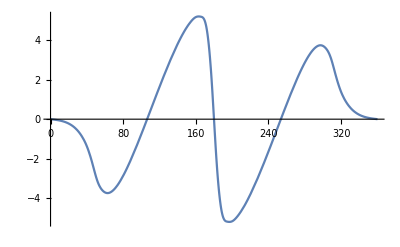

{x→106.373}

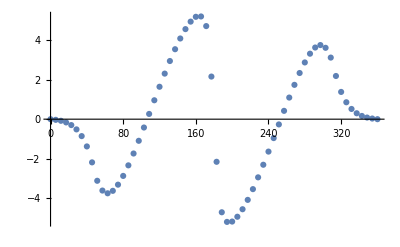

```mathematica
Points= Transpose[{thetas/Degree,Txs}];
f=Interpolation[Points,Method->"Spline"]
Plot[f[x],{x,0,360}]
FindRoot[f[x],{x,100}]
ListPlot[Points,Joined->False]
```

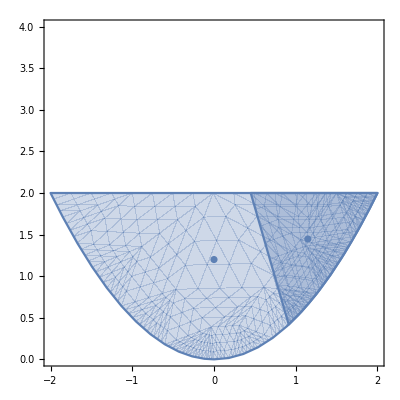

```mathematica
ReleaseHold[Hold[Show[
RegionPlot[BoatRegion[n]],
RegionPlot[EqRegion[n,θ Degree]],
ListPlot[{CoB[n,θ Degree],CoM[n]}]
,PlotRange->{{-2,2},{0,4}}
]]/.{θ->106.373,n->2}]
```

```mathematica
(*1,2*)
BoatSurface[D_,L_,B_]:=D*((2#1/L)^4+(2#2/B)^2)&
BoatSurface[D,L,B][x,y]
Manipulate[
RegionPlot3D[D>z>BoatSurface[B,D,L][x,y],{x,-1,1},{y,-1,1},{z,0,2},AxesLabel->Automatic]
,{B,.001,2},{D,.001,2},{L,.001,2}]
(*L controls the length of the boat along y, B controls the width of the boat along x (inversly) while also slightly affecting the length, and D controls the scale of the boat along z, as well as the height of the boat.*)
```

D ((16 x^4)/L^4+(4 y^2)/B^2)

RegionPlot3D::boolf: 0.624>z>BoatSurface[0.37,0.624,1.132][x,y] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

z==(4 B y^2)/L^2

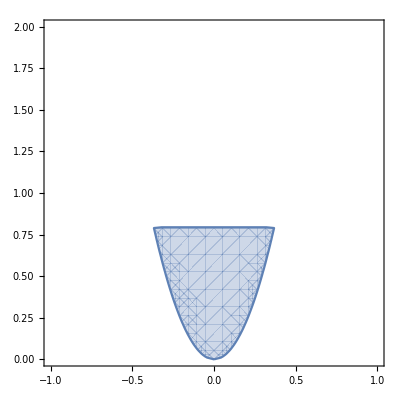

```mathematica
(*3*)
(*a*)z==BoatSurface[B,D,L][0,y]
RegionPlot[{z>BoatSurface[0.032,0.804,0.148][0,y]&&z<0.794},{y,-1,1},{z,0,2}]
```

```mathematica
(*b*)
```

z==B (6.5536/D^4+(4 y^2)/L^2)

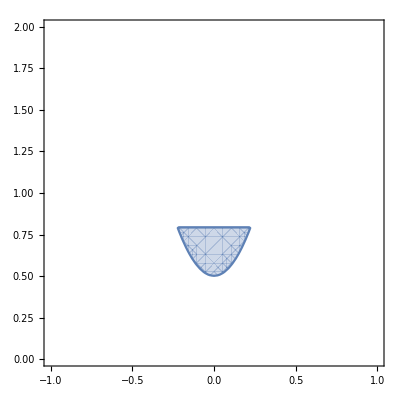

```mathematica
z==BoatSurface[B,D,L][0.8,y]
RegionPlot[{z>BoatSurface[0.032,0.804,0.148][0.8,y]&&z<0.794},{y,-1,1},{z,0,2}]
```

z==(16 B x^4)/D^4

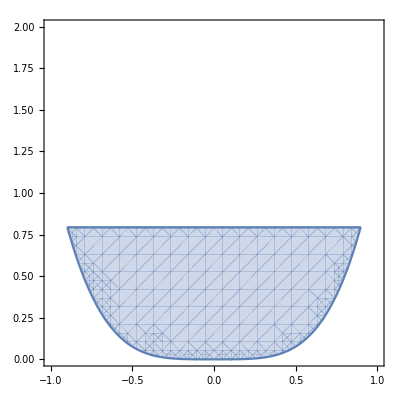

```mathematica
(*c*)
z==BoatSurface[B,D,L][x,0]
RegionPlot[{z>BoatSurface[0.032,0.804,0.148][x,0]&&z<0.794},{x,-1,1},{z,0,2}]
```

(16 x^4)/B^4+(4 y^2)/L^2==1

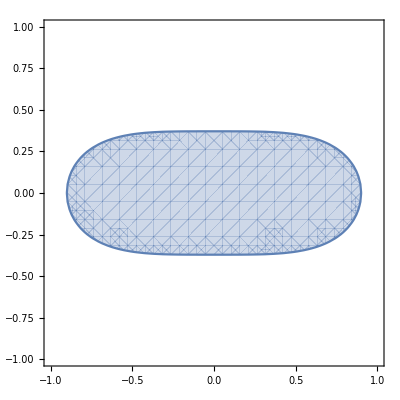

```mathematica
(*d*)
Simplify[BoatSurface[D,B,L][x,y]/D==D/D]
RegionPlot[BoatSurface[0.032,0.804,0.148][x,y]<0.804,{x,-1,1},{y,-1,1}]
```

```mathematica
(*4*)
(r1*M1+r2*M2+r3*M3)/(M1+M2+M3)
```

(M1 r1+M2 r2+M3 r3)/(M1+M2+M3)

```mathematica
(*5*)
(r1*M1+(r1+p12)*M2+(r1+p13)*M3)/(M1+M2+M3)
```

(M1 r1+M2 (p12+r1)+M3 (p13+r1))/(M1+M2+M3)